# Exploring the COVID-19 Wolfram Data Repository

The datasets on the COVID-19 pandemic are updated regularly.  Please take note of this as the data available at the time of this recording will be different from yours.

Wolfram Alpha has information on the virus.  We simply pass the string “Coronavirus” as argument to the WolframAlpha function.

```mathematica
WolframAlpha["Coronavirus"];
```

We can view what datasets are available in the Wolfram data Repository using the ResourceSearch function.

```mathematica
ResourceSearch["Coronavirus"]
```

Dataset[<>]

There are three datasets.  One each on epidemic data, genetic sequence data, and patient medical data.  In this video, we will take a look at the medical data and in the next, the epidemiological data.

## Importing the patient medical dataset

The Patient Medical Data for Novel Coronavirus COVID-19 dataset provides information on the gender of infected patients, as well as the city and country where they were diagnosed.  There is also data on the date of onset of symptoms and the date of confirmation of disease.  A list object of symptoms is available for some patients in the Symptoms column.  The rest of the dataset contains sparse information as this is an ongoing pandemic.

```mathematica
medicalData=ResourceData["Patient Medical Data for Novel Coronavirus COVID-19"]
```

Dataset[<>]

We can retrieve a list of all the variables (column names / column headers) using the Keys function.

```mathematica
Normal[medicalData[1,Keys]](*Express the variables as a list object*)
```

{Age,Sex,City,AdministrativeDivision,Country,GeoPosition,DateOfOnsetSymptoms,DateOfAdmissionHospital,DateOfConfirmation,Symptoms,LivesInWuhan,LivesInWuhanComment,TravelHistoryDates,TravelHistoryLocation,ReportedMarketExposure,ReportedMarketExposureComment,ChronicDiseaseQ,ChronicDiseases,SequenceAvailable,DischargedQ,DeathQ,DateOfDeath,DateOfDischarge}

We can learn more about the data resource.

```mathematica
medDataResource=ResourceObject["Patient Medical Data for Novel Coronavirus COVID-19"]
```

ResourceObject[…]

These are the properties we can learn more about.

```mathematica
medDataResource["Properties"]
```

{AutoUpdate,Categories,ContentElementLocations,ContentElements,ContentSize,ContentTypes,ContributedBy,ContributorInformation,DefaultContentElement,Description,Details,DocumentationLink,DOI,DownloadedVersion,ExampleNotebook,ExampleNotebookObject,Format,InformationElements,Keywords,LatestUpdate,Name,Originator,Properties,ReleaseDate,RepositoryLocation,ResourceLocations,ResourceType,SeeAlso,ShortName,SourceMetadata,Title,UUID,Version,WolframLanguageVersionRequired}

```mathematica
Manipulate[medDataResource[n],{n,medDataResource["Properties"]}]
```

The countries and provinces / cities are created as Wolfram Language entities.  We can express these using the Interpreter function.

```mathematica
usa=Interpreter["Country"]["United States"]
```

United States

## Age analysis

Age seems to be important as a risk factor for mortality.  Below, we create a histogram of the age distribution of all the patients.  First, we extract all the age values that were captures as integers.

Using the Cases function with the _Integer argument ensures that we only select the cases in which the actual ages were captured.

```mathematica
allAges=Cases[Normal[medicalData[All,"Age"]],_Integer];
```

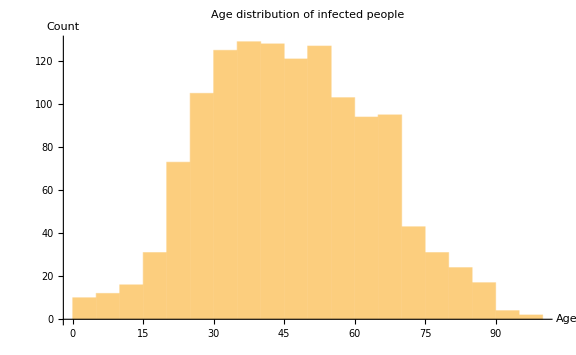

```mathematica
Histogram[allAges,PlotLabel->"Age distribution of infected people",AxesLabel->{"Age","Count"},ImageSize->Large]
```

A binary sample space exists for gender.

```mathematica
DeleteDuplicates[medicalData[All,"Sex"]]
```

Dataset[<>]

We can compare the age difference between these binary genders.

```mathematica
(*Extracting the entities for the two genders*)
male=Entity["Gender","Male"];
female=Entity["Gender","Female"];
```

```mathematica
female
```

female

```mathematica
(*Saving two seperate list objects*)
femaleAge=Normal[Cases[Select[medicalData,#Sex==female&]⟦;;,"Age"⟧,_Integer]];(*Integer values only*)
maleAge=Normal[Cases[Select[medicalData,#Sex==male&]⟦;;,"Age"⟧,_Integer]];
```

```mathematica
PairedHistogram[Labeled[femaleAge,"Female",Left],Labeled[maleAge,"Male",Right],PlotLabel->"Comparison of age distribution between genders",ImageSize->Large]
```

-Graphics-

## Symptoms

There are many symptoms captured as list objects.  We can extract them as an association object using the Counts function.

```mathematica
symptoms=Sort[Counts[DeleteMissing[Flatten[Normal[medicalData⟦All,"Symptoms"⟧]]]],Greater]
```

<|fever→430,cough→236,sore throat→39,fatigue→36,shortness of breath→28,rhinorrhea→25,myalgias→25,malaise→23,headache→22,chills→21,pneumonitis→20,sputum→19,chest pain→19,pneumonia→17,weakness→12,bone pain→10,diarrhea→10,respiratory symptoms→10,asymptomatic→9,sneezing→8,joint pain→7,nausea→7,vomiting→6,pharyngalgia→6,gasp→4,body soreness→4,38°C→4,dry throat→4,37°C→3,anorexia→3,dry mouth→3,acute respiratory viral infection→3,flu-like symptoms→3,dizziness→3,37.5°C→2,37.7°C→2,38.3°C→2,abdominal pain→2,37.1°C→2,conjunctivitis→2,cold symptoms→2,sore muscle→2,other symptoms→2,primary myelofibrosis→1,somnolence→1,afebrile→1,difficulty walking→1,39°C→1,similar to a respiratory infection→1,37.2°C→1,toothache→1,37.8°C→1,discharge→1,38.1°C→1,acute pharyngitis→1,esophageal reflux→1,no respiratory symptoms→1,39.3°C→1,38.2°C→1,poor physical condition→1,full body slump→1,wheezing→1,sweating→1,acute coronary syndrome→1,acute left heart failure→1,lesions on chest radiographs→1,sore limbs→1,lack of energy→1,systemic weakness→1,soreness→1,pleural effusion→1|>

Since we have sorted the symptoms in descending order, a word cloud of the most common symptoms provides a good visualization of this data.

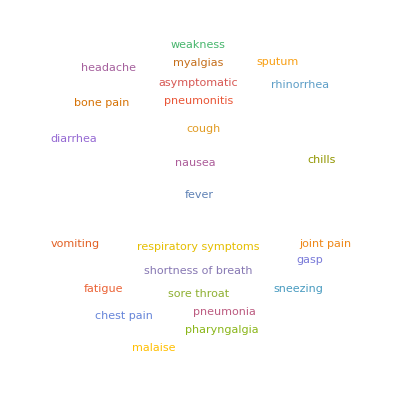

```mathematica
WordCloud[symptoms⟦;;25⟧]
```

## Timelines

The dates in the dataset are Wolfram Language date objects.  We can therefor use them with the TimelinePlot.

```mathematica
usaMedicalData=medicalData[Select[#Country==usa&]]
```

Dataset[<>]

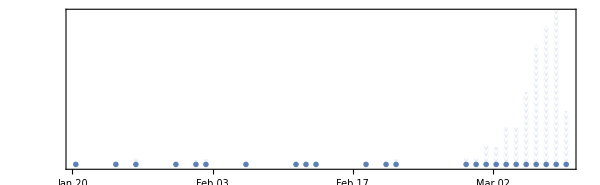

```mathematica
TimelinePlot[usaMedicalData⟦All,"DateOfConfirmation"⟧]
```

We can also look at an individual patient.  Below we plot the dates of onset of symptoms, hospital admission, and conformation of infection.

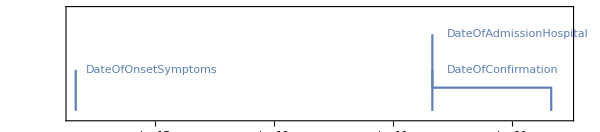

```mathematica
TimelinePlot[usaMedicalData⟦2,{"DateOfOnsetSymptoms","DateOfAdmissionHospital","DateOfConfirmation"}⟧]
```

Below, we extract the data for all patients for which we know the age, gender, onset of symptoms and death.

```mathematica
symptomToDeathTL=medicalData[Select[(!MissingQ[#Age]&&!MissingQ[#Sex]&&!MissingQ[#DateOfOnsetSymptoms]&&!MissingQ[#DateOfDeath])&],{"Age","Sex","DateOfOnsetSymptoms","DateOfDeath"}]
```

Dataset[<>]

Below, we create a grid of the first 10 people.

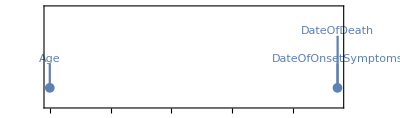
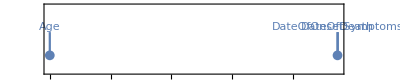
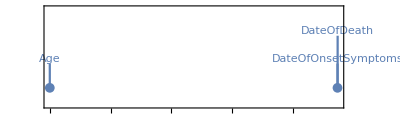
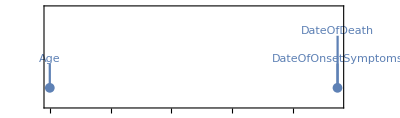
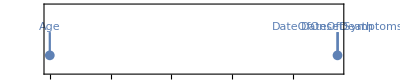
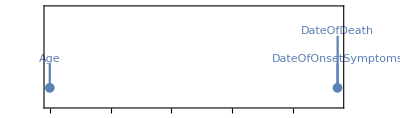
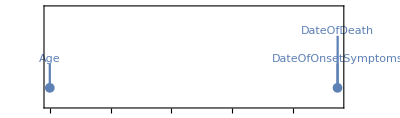
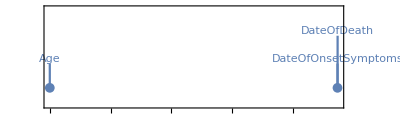
-Graphics-36 yrs old male | -Graphics-48 yrs old female
-Graphics-53 yrs old male | -Graphics-55 yrs old male
-Graphics-58 yrs old male | -Graphics-58 yrs old male
-Graphics-61 yrs old male | -Graphics-65 yrs old male
-Graphics-65 yrs old male | -Graphics-66 yrs old female

```mathematica
Grid[Partition[Labeled[TimelinePlot[Take[#,4],PlotRange->{"Dec 20 2019","March 10 2020"},ImageSize->Medium],StringTemplate["`Age` yrs old `Sex`"][#],Bottom]&/@Normal[Sort[symptomToDeathTL]]⟦;;10⟧,2],Alignment->{{Left,Left},{Bottom,Bottom}}]
```

Of great interest is the time difference between the onset of symptoms and confirmation.  There are many factors at play here.  They include patient factors and the availability of resources.

```mathematica
differenceSymptomsConfirmation=medicalData[Select[(!MissingQ[#DateOfOnsetSymptoms]&&!MissingQ[#DateOfConfirmation])&],DateDifference[#DateOfOnsetSymptoms,#DateOfConfirmation]&]
```

Dataset[<>]

We need to know for how many cases this data is available.

```mathematica
Length[differenceSymptomsConfirmation]
```

839

A histogram shows  the distribution of this delay.  There are some incorrect dates, so we select only the positive days.  Since the time unit (days) are captured with the calculation of the difference in dates, we need to remove it with the QuantityMagnitude function.

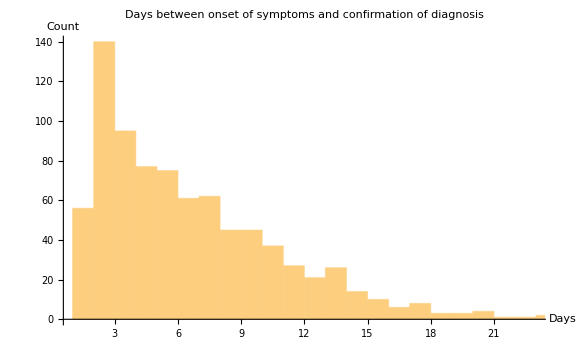

```mathematica
Histogram[Select[QuantityMagnitude@differenceSymptomsConfirmation,#>0&],PlotLabel->"Days between onset of symptoms and confirmation of diagnosis",AxesLabel->{"Days","Count"},ImageSize->Large]
```

There might be a difference between onset of symptoms and confirmation between the binary genders.  We extract only the relevant columns and create two dataset objects, one for each gender.

```mathematica
femaleDates=Select[medicalData,#Sex==female&]⟦;;,{"DateOfOnsetSymptoms","DateOfConfirmation"}⟧;
maleDates=Select[medicalData,#Sex==male&]⟦;;,{"DateOfOnsetSymptoms","DateOfConfirmation"}⟧;
```

Now, we create a list of days for each.

```mathematica
femaleDifference=QuantityMagnitude@Normal@femaleDates[Select[(!MissingQ[#DateOfOnsetSymptoms]&&!MissingQ[#DateOfConfirmation])&],DateDifference[#DateOfOnsetSymptoms,#DateOfConfirmation]&];
maleDifference=QuantityMagnitude@Normal@maleDates[Select[(!MissingQ[#DateOfOnsetSymptoms]&&!MissingQ[#DateOfConfirmation])&],DateDifference[#DateOfOnsetSymptoms,#DateOfConfirmation]&];
```

A box-and-whisker plot with outliers will show us the difference.

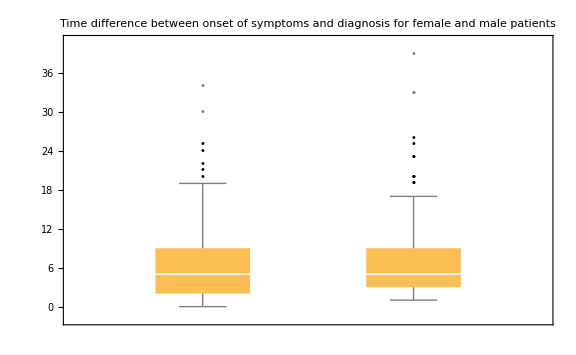

```mathematica
BoxWhiskerChart[{femaleDifference,Select[maleDifference,#>0&]},"Outliers",PlotLabel->"Time difference between onset of symptoms and diagnosis for female and male patients",ImageSize->Large]
```

The data is clearly not from a population in which the values are normally distributed.  To compare, let’s use a non-parametric test.

```mathematica
MannWhitneyTest[{femaleDifference,Select[maleDifference,#>0&]},0,"TestDataTable"]
```

| Statistic | P-Value
Mann-Whitney | 78643. | 0.686372

## Geographical position data

The GeoPosition column provides data that we can plot, using the GeoGraphics function.

```mathematica
medicalData⟦1;;5,"GeoPosition"⟧(*Listing the first five geographic locations*)
```

Dataset[<>]

```mathematica
GeoGraphics[{GeoMarker[medicalData⟦1;;5,"GeoPosition"⟧]}](*Plotting the first five geographic locations in the dataset*)
```

-Graphics-

We can plot all the cases for a single country such as the United States.

```mathematica
GeoGraphics[{Red,GeoMarker[usaMedicalData⟦All,"GeoPosition"⟧]}](*Listing geographic locations of all USA cases*)
```

-Graphics-

We can be more precise.  Fits, we select only the cases where the geological position is known.

```mathematica
DeleteMissing@Normal@usaMedicalData[Select[!MissingQ[#GeoPosition]&],#GeoPosition->#City&]
```

{GeoPosition[{41.8781,-87.6298}]→Chicago,GeoPosition[{34.05,-118.25}]→Los Angeles,GeoPosition[{33.4128,-111.943}]→Tempe,GeoPosition[{41.8781,-87.6298}]→Chicago,GeoPosition[{42.3601,-71.0589}]→Boston,GeoPosition[{43.0849,-89.5465}]→Madison,GeoPosition[{40.661,-73.944}]→New York City,GeoPosition[{47.6097,-122.333}]→Seattle,GeoPosition[{47.6097,-122.333}]→Seattle,GeoPosition[{47.6097,-122.333}]→Seattle,GeoPosition[{47.6097,-122.333}]→Seattle,GeoPosition[{47.6097,-122.333}]→Seattle,GeoPosition[{47.6097,-122.333}]→Seattle,GeoPosition[{47.6097,-122.333}]→Seattle,GeoPosition[{40.9086,-73.7819}]→New Rochelle,GeoPosition[{40.9086,-73.7819}]→New Rochelle,GeoPosition[{40.9086,-73.7819}]→New Rochelle,GeoPosition[{40.9086,-73.7819}]→New Rochelle,GeoPosition[{40.9086,-73.7819}]→New Rochelle,GeoPosition[{41.8756,-71.3761}]→Pawtucket,GeoPosition[{41.8756,-71.3761}]→Pawtucket,GeoPosition[{27.9681,-82.4764}]→Tampa,GeoPosition[{27.9681,-82.4764}]→Tampa,GeoPosition[{42.2964,-71.2931}]→Wellesley,GeoPosition[{42.3601,-71.0589}]→Boston,GeoPosition[{42.3601,-71.0589}]→Boston,GeoPosition[{42.3601,-71.0589}]→Boston,GeoPosition[{41.8781,-87.6298}]→Chicago,GeoPosition[{37.8717,-122.273}]→Berkeley,GeoPosition[{34.05,-118.25}]→Los Angeles,GeoPosition[{34.05,-118.25}]→Los Angeles,GeoPosition[{34.05,-118.25}]→Los Angeles,GeoPosition[{34.05,-118.25}]→Los Angeles,GeoPosition[{34.05,-118.25}]→Los Angeles,GeoPosition[{37.3544,-121.969}]→Santa Clara,GeoPosition[{37.3544,-121.969}]→Santa Clara,GeoPosition[{37.3544,-121.969}]→Santa Clara,GeoPosition[{37.7775,-122.416}]→San Francisco,GeoPosition[{37.7775,-122.416}]→San Francisco,GeoPosition[{32.715,-117.163}]→San Diego,GeoPosition[{34.05,-118.25}]→Los Angeles,GeoPosition[{34.05,-118.25}]→Los Angeles,GeoPosition[{34.05,-118.25}]→Los Angeles,GeoPosition[{34.05,-118.25}]→Los Angeles,GeoPosition[{39.5272,-119.822}]→Reno,GeoPosition[{40.851,-73.971}]→Fort Lee,GeoPosition[{29.425,-98.4939}]→San Antonio,GeoPosition[{29.425,-98.4939}]→San Antonio,GeoPosition[{29.7628,-95.3831}]→Houston,GeoPosition[{47.7564,-122.34}]→Shoreline,GeoPosition[{47.5356,-122.043}]→Issaquah,GeoPosition[{38.7197,-77.1546}]→Fort Belvoir,GeoPosition[{39.9833,-75.2664}]→Lower Merion township,GeoPosition[{39.9833,-75.2664}]→Lower Merion township,GeoPosition[{47.6097,-122.333}]→Seattle,GeoPosition[{47.6097,-122.333}]→Seattle,GeoPosition[{47.6097,-122.333}]→Seattle,GeoPosition[{34.05,-118.25}]→Los Angeles,GeoPosition[{37.7775,-122.416}]→San Francisco,GeoPosition[{37.7775,-122.416}]→San Francisco,GeoPosition[{37.7775,-122.416}]→San Francisco,GeoPosition[{37.7775,-122.416}]→San Francisco,GeoPosition[{37.7775,-122.416}]→San Francisco,GeoPosition[{37.7775,-122.416}]→San Francisco,GeoPosition[{38.6272,-90.1978}]→Saint Louis,GeoPosition[{38.0297,-84.4947}]→Lexington,GeoPosition[{32.7833,-79.9333}]→Charleston,GeoPosition[{42.3601,-71.0589}]→Boston,GeoPosition[{40.661,-73.944}]→New York City,GeoPosition[{40.661,-73.944}]→New York City,GeoPosition[{40.661,-73.944}]→New York City,GeoPosition[{40.661,-73.944}]→New York City,GeoPosition[{40.661,-73.944}]→New York City,GeoPosition[{40.661,-73.944}]→New York City,GeoPosition[{40.661,-73.944}]→New York City,GeoPosition[{40.661,-73.944}]→New York City,GeoPosition[{40.661,-73.944}]→New York City,GeoPosition[{40.661,-73.944}]→New York City,GeoPosition[{40.661,-73.944}]→New York City,GeoPosition[{40.661,-73.944}]→New York City,GeoPosition[{40.661,-73.944}]→New York City,GeoPosition[{40.661,-73.944}]→New York City,GeoPosition[{40.661,-73.944}]→New York City,GeoPosition[{40.661,-73.944}]→New York City,GeoPosition[{40.661,-73.944}]→New York City}

We can look at NYC.

```mathematica
nyc=Interpreter["City"]["New York"]
```

New York City

Let’s see where in NYC the cases were reported.  We will look at a 50 miles radius.

```mathematica
GeoGraphics[Tooltip[GeoMarker[#⟦1⟧],CommonName[#⟦2⟧]]&/@DeleteMissing@Normal@usaMedicalData[Select[!MissingQ[#GeoPosition]&],#GeoPosition->#City&],GeoCenter->nyc,GeoRange->Quantity[50,"Miles"],ImageSize->Large]
```

-Graphics-

## Mortality

Complete data on mortality is not available for this dataset.

```mathematica
Counts@Normal@medicalData⟦All,"DeathQ"⟧
```

<|Missing[NotAvailable]→40543,True→46|>

For the data that is available, though, we are interested in the association between mortality and comorbid disease.

```mathematica
comorbid=medicalData[Select[!MissingQ[#ChronicDiseaseQ]&&!MissingQ[#DeathQ]&],{"ChronicDiseaseQ","DeathQ","ChronicDiseases"}]
```

Dataset[<>]

The top chronic diseases for those who died and have had chronic disease listed can now be calculated.

```mathematica
Sort[Counts[DeleteMissing[Normal[Flatten[comorbid⟦All,"ChronicDiseases"⟧]]]],Greater]
```

<|hypertension→14,diabetes→11,coronary heart disease→4,chronic bronchitis→3,Parkinson's disease→2,coronary stent→2,cerebral infarction→2,tuberculosis→1,hemorrhage of digestive tract→1,stenocardia→1,colon cancer→1,hip replacement→1,encephalomalacia→1,frequent ventricular premature beat→1,chronic renal insufficiency→1,chronic obstructive pulmonary disease→1|>

There might be a significant difference in the ages between those who have died and those who are alive.

```mathematica
ageAlive=medicalData[Select[!MissingQ[#Age]&&MissingQ[#DeathQ]&],{"Age","DeathQ"}];
ageDead=medicalData[Select[!MissingQ[#Age]&&!MissingQ[#DeathQ]&],{"Age","DeathQ"}];
```

```mathematica
aliveAge=Normal[Cases[ageAlive⟦All,"Age"⟧,_Integer]];
deadAge=Normal[Cases[ageDead⟦All,"Age"⟧,_Integer]];
```

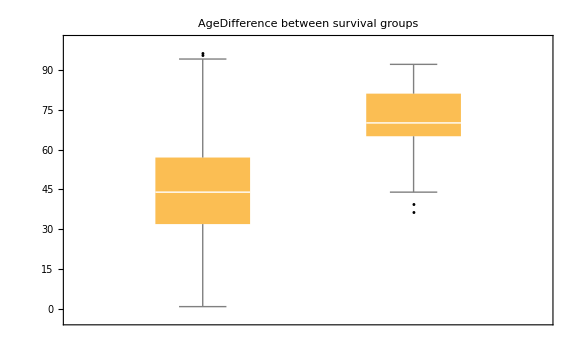

```mathematica
BoxWhiskerChart[{aliveAge,deadAge},"Outliers",PlotLabel->"AgeDifference between survival groups",ImageSize->Large]
```

There is clearly a significant difference in these age groups.  We use a non-parametric test to compare the two groups.

```mathematica
MannWhitneyTest[{aliveAge,deadAge},0,"TestDataTable"]
```

| Statistic | P-Value
Mann-Whitney | 6801. | 2.9836×10^-16